```mathematica
FileExport[data_, filename_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,StringJoin[filename, ".pdf"]}] , data, "PDF"];
];
```

```mathematica
visualFrame = Plot[0, {x, 0, 0.1}, 
AxesOrigin->{0.5, 0},
GridLines->{{1, 1.5, 2}, {1, 2}},
PlotStyle->{Dashed, Black, Thin}, 
 TicksStyle-> Directive[Black,FontFamily -> "Times", 18], 
Ticks-> {{}, {}},
 AxesLabel->{"x", "t"}, 
AxesStyle->  Directive[Black, FontFamily-> "Times",17],
PlotRange->Full,
ImageSize->600
];
```

```mathematica
visualLabels = Graphics[{
Text[Style["x_(i - FractionBox[1, 2])", FontFamily->"Times", 16], {1, -0.1}],
Text[Style["x_(i + FractionBox[1, 2])", FontFamily->"Times", 16], {1.5, -0.1}],
Text[Style["x_(i + FractionBox[3, 2])", FontFamily->"Times", 16], {2, -0.1}],
Text[Style["t", FontFamily->"Times", 16], {0.45, 0.95}],
Text[Style["t + τ", FontFamily->"Times", 16], {0.4, 1.95}],
Text[Style["i", FontFamily->"Times", 16, Bold], {1.25, 2.1}],
Text[Style["i + 1", FontFamily->"Times", 16, Bold], {1.75, 2.1}]
}];
visualLines = Graphics[{
Text[Style["3", FontFamily->"Times", 16], {1.5, 2.08}],

PointSize[0.01],
Point[{1.5, 2}],
Point[{1.25, 1}],
Line[{{1.5, 2}, {1.25, 1}}],
Text[Style["1", FontFamily->"Times", 16], {1.23, 1.08}],
Text[Style["x_p_1", FontFamily->"Times", 16], {1.3, 1.5}],

Point[{1.95, 1}],
Line[{{1.5, 2}, {1.95, 1}}],
Text[Style["2", FontFamily->"Times", 16], {1.98, 1.08}],
Text[Style["x_p_2", FontFamily->"Times", 16], {1.85, 1.5}],

Dashed,
Thick,
Red,
Line[{{1.25, 1}, {1.495, 1}}],
Thickness -> 0.003,
Dashing-> None,
Line[{{1.25, 1}, {1.25, 0.875}}],
Line[{{1.495, 1}, {1.495, 0.875}}],
Text[Style["λ_p_1τ", FontFamily->"Times", 16], {1.38, 0.9}],

Thick,
Blue,
Dashed,
Line[{{1.505, 1}, {1.95, 1}}],
Thickness -> 0.003,
Dashing-> None,
Line[{{1.505, 1}, {1.505, 0.875}}],
Line[{{1.95, 1}, {1.95, 0.875}}],
Text[Style["λ_p_2τ", FontFamily->"Times", 16], {1.75, 0.9}],
}];
```

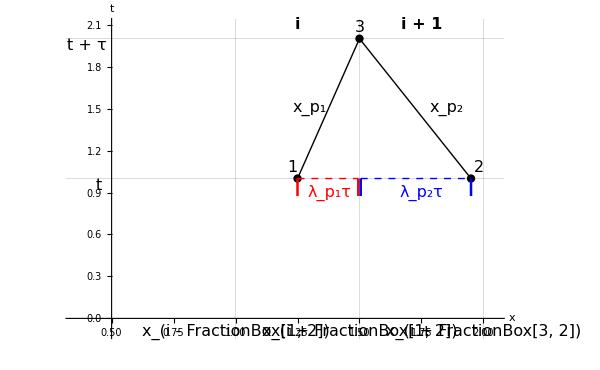

```mathematica
visual=Show[visualFrame, visualLabels,visualLines, PlotRange-> {{0.35, 2.05}, Full }]
```

```mathematica
FileExport[visual, "visualization"]
```

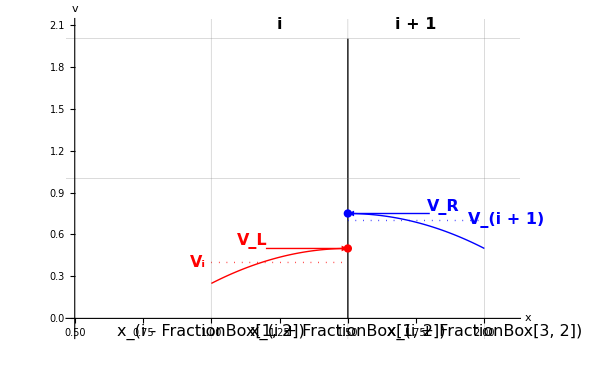

```mathematica
approximationFrame = Plot[0, {x, 0, 0.1},
AxesOrigin->{0.5, 0},
GridLines->{{1, 1.5, 2}, {1, 2}},
PlotStyle->{Thick, Black}, 
 TicksStyle-> Directive[Black,FontFamily -> "Times", 18], 
Ticks-> {{}, {}},
 AxesLabel->{"x", "v"}, 
AxesStyle->  Directive[Black, FontFamily-> "Times",17],
PlotRange->All,
ImageSize->600
];
approximationLabels = Graphics[{
Text[Style["x_(i - FractionBox[1, 2])", FontFamily->"Times", 16], {1, -0.1}],
Text[Style["x_(i + FractionBox[1, 2])", FontFamily->"Times", 16], {1.5, -0.1}],
Text[Style["x_(i + FractionBox[3, 2])", FontFamily->"Times", 16], {2, -0.1}],
Text[Style["i", FontFamily->"Times", 16, Bold], {1.25, 2.1}],
Text[Style["i + 1", FontFamily->"Times", 16, Bold], {1.75, 2.1}]
}];
approximationLPlot = Plot [-(x-1.5)^2 + 0.5, {x, 1, 1.5}, PlotStyle->{Thick, Red}];
approximationRPlot =  Plot [-(x-1.5)^2 + 0.75, {x, 1.5, 2}, PlotStyle->{Thick, Blue}];
approximationLines = Graphics[{
Thick,
Line[{{1.5, 2},{1.5, 0}}],
Arrowheads[0.025],
PointSize-> 0.01,

Dotted,
Red,
Line[{{1, 0.4},{1.5, 0.4}}],
Point[{1.5, 0.5}],
Text[Style["V_i", FontFamily->"Times", 16, Bold], {0.95, 0.4}],
Dashing-> None,
Arrow[{{1.2, 0.5},{1.5, 0.5}}],
Text[Style["V_L", FontFamily->"Times", 16, Bold], {1.15, 0.55}],


Dotted,
Blue,
Line[{{1.5, 0.7},{2, 0.7}}],
Point[{1.5, 0.75}],
Text[Style["V_(i + 1)", FontFamily->"Times", 16, Bold], {2.08, 0.7}],
Dashing-> None,
Arrow[{{1.8, 0.75},{1.5, 0.75}}],
Text[Style["V_R", FontFamily->"Times", 16, Bold], {1.85, 0.8}],
}];
approximation = Show[approximationFrame,approximationLabels, approximationLPlot, approximationRPlot,approximationLines,PlotRange-> {{0.5, 2.1}, {-0.1, 2.1} }]
```

```mathematica
FileExport[approximation, "approximation"];
```